<|
"Title"→"Replacement Patterns",
"Slug"→Automatic,
"Path"→"Mathematica Programming/Code Structure",
"ID"→{"2.1.4"},
"Date"→Now,
"Modified"→Now,
"Authors"→{},
"Categories"→{"mathematica-programming","code-structure"},
"Tags"→{"patterns"}
|>

### Replacement Patterns

The fundamental usage of patterns is in replacement. This is just what it sounds like. One replaces part of an expression with something else. There’s a whole family of functions built around this concept, too, and they’re some of the oldest functions in the language. They all share one parent, though

#### Replace

Replace is possibly the most fundamental function in Mathematica. It takes an expression and if it matches a pattern, replaces it with that value. For example:

```mathematica
Replace[{1,2,3},a:{__Integer}:>Column@a]
```

1
2
3

If the pattern doesn’t match, nothing happens:

```mathematica
Replace[{1,2,3},
	a:{RandomInteger[1000],RandomReal[1000],RandomReal[1000]}:>
		"This has a 1/1000000000 chance of being the result"
	]
```

{1,2,3}

Replace can also try a list of replacements:

```mathematica
Replace[{1,2,3},
	{
		{_Integer,_Integer,_String}:>"No",
		{_Integer,_Integer,_List}:>"No",
		{_Integer,_Integer,_Association}:>"No",
		{_Integer,_Integer,_Integer}:>"Yes!",
		{__Integer}:>"Yes, but won't happen"
		}
	]
```

Yes!

You’ll notice it only matches the first pattern that fits.

Replace can also work at various levels of an expression:

```mathematica
Replace[{1,2,"3",2,1},
	i_Integer:>("int "<>ToString@i),
	1]
```

{int 1,int 2,3,int 2,int 1}

#### ReplaceAll

ReplaceAll is the only other member of the family I’ll mention here. It works similarly to Replace, except the replacements can happen at any level of the expression. This is dangerous, but also useful.

Also useful is the fact that it has a keyboard alias: /.

Here’s a fun example:

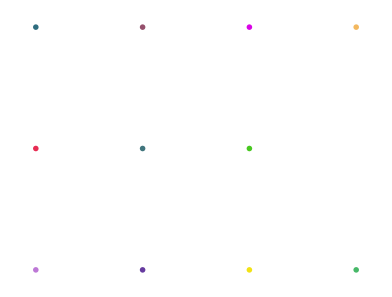

```mathematica
GraphicsGrid[
	Table[
		Table[RandomInteger[100],
			{j, RandomInteger[{1,6}]}],
		{i,RandomInteger[{3,5}]}
		]/.i_Integer:>Graphics[{RandomColor[],Disk[]}, ImageSize->i],
	Spacings->0
	]
```

#### Replace⋆

The rest of this family share the name Replace⋆ and most of them work quite like Replace, with the notable exception of ReplacePart